```mathematica
Clear["Global`*"]
```

```mathematica
L = 30 10^8;
Δtr = 3 10^8;
Δch = 5 10^8;
w = 0.75 10^8;
A = 0.1;
Tco = 2 10^6;
Tch = 2 10^4;
```

```mathematica
S[x_] = Piecewise[{{1 - (x/w - 1)^2,0 < x && x < 2w},{0,{0 >= x || x >= 2w}}}]
```

Piecewise[{{1-(-1+1.33333×10^-8 x)^2, 0<x&&x<1.5×10^8}, {0, True}}]

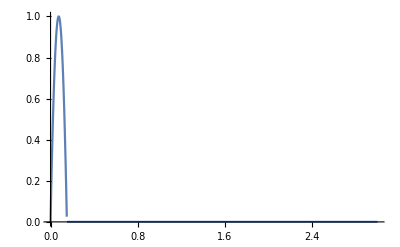

```mathematica
Plot[S[s],{s,0,L}]
```

```mathematica
Heq[l_]:= A(S[l - Δtr-Δch] - S[l-Δch] + S[L-Δtr-Δch-l] - S[L-l-Δch])
```

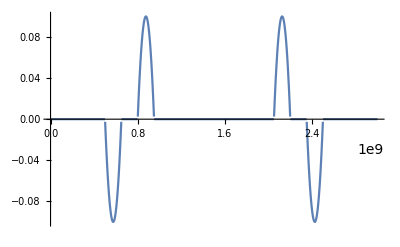

```mathematica
Plot[Heq[s],{s,0,L}]
```

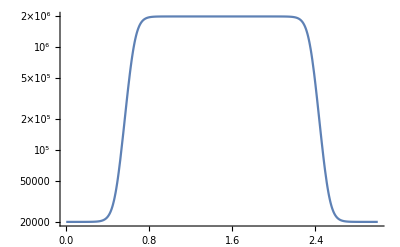

```mathematica
Teq[l_]:= Tch +(Tco-Tch)/2(Tanh[(4(l - Δch-(Δtr - 2w)))/Δtr]+Tanh[(4(L-l - Δch-(Δtr - 2w)))/Δtr])
LogPlot[Teq[s],{s,0,L},PlotRange->{1000,All}]
```

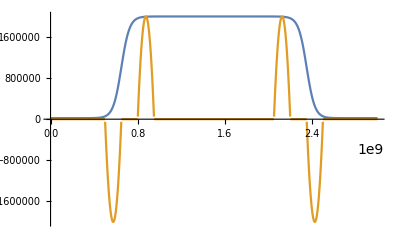

```mathematica
Plot[{Teq[s],10Tco Heq[s]},{s,0,L}]
```